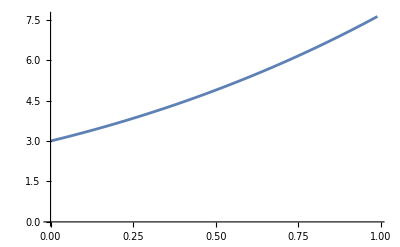

```mathematica
data = {{0,3},{0.01,3.03},{0.02,3.0603},{0.03,3.0909},{0.04,3.1218},{0.05,3.153},{0.06,3.1845},{0.07,3.21631},{0.08,3.24843},{0.09,3.28085},{0.1,3.31358},{0.11,3.34661},{0.12,3.37996},{0.13,3.41361},{0.14,3.44758},{0.15,3.48186},{0.16,3.51645},{0.17,3.55136},{0.18,3.58659},{0.19,3.62213},{0.2,3.65799},{0.21,3.69417},{0.22,3.73067},{0.23,3.76749},{0.24,3.80464},{0.25,3.84211},{0.26,3.8799},{0.27,3.91803},{0.28,3.95648},{0.29,3.99526},{0.3,4.03437},{0.31,4.07381},{0.32,4.11359},{0.33,4.1537},{0.34,4.19415},{0.35,4.23494},{0.36,4.27606},{0.37,4.31753},{0.38,4.35933},{0.39,4.40148},{0.4,4.44398},{0.41,4.48681},{0.42,4.53},{0.43,4.57354},{0.44,4.61742},{0.45,4.66166},{0.46,4.70625},{0.47,4.7512},{0.48,4.7965},{0.49,4.84216},{0.5,4.88819},{0.51,4.93457},{0.52,4.98131},{0.53,5.02842},{0.54,5.0759},{0.55,5.12374},{0.56,5.17195},{0.57,5.22054},{0.58,5.26949},{0.59,5.31882},{0.6,5.36853},{0.61,5.41862},{0.62,5.46908},{0.63,5.51993},{0.64,5.57116},{0.65,5.62277},{0.66,5.67478},{0.67,5.72717},{0.68,5.77995},{0.69,5.83313},{0.7,5.8867},{0.71,5.94066},{0.72,5.99503},{0.73,6.04979},{0.74,6.10496},{0.75,6.16054},{0.76,6.21652},{0.77,6.27291},{0.78,6.32971},{0.79,6.38692},{0.8,6.44455},{0.81,6.50259},{0.82,6.56106},{0.83,6.61995},{0.84,6.67926},{0.85,6.73899},{0.86,6.79916},{0.87,6.85975},{0.88,6.92078},{0.89,6.98224},{0.9,7.04415},{0.91,7.10649},{0.92,7.16927},{0.93,7.2325},{0.94,7.29618},{0.95,7.3603},{0.96,7.42488},{0.97,7.48991},{0.98,7.5554},{0.99,7.62135}};
ListPlot[data, Joined->True]
```

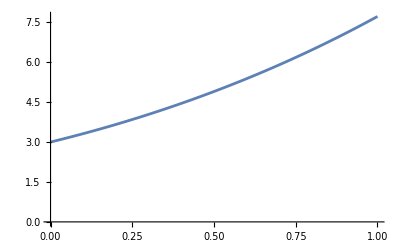

```mathematica
sol = DSolve[{y'[x]==y[x]-x^2, y[0]==3}, y[x], x];
Plot[Evaluate[y[x]/.sol], {x, 0, 1}, AxesOrigin->{0,0}]
```

```mathematica
table=Table[{x,y[x]/. sol/. {val_}:>val},{x,0,1,0.01}];
Grid[table]
```

0. | 3.
0.01 | 3.03015
0.02 | 3.0606
0.03 | 3.09135
0.04 | 3.12241
0.05 | 3.15377
0.06 | 3.18544
0.07 | 3.21741
0.08 | 3.24969
0.09 | 3.28227
0.1 | 3.31517
0.11 | 3.34838
0.12 | 3.3819
0.13 | 3.41573
0.14 | 3.44987
0.15 | 3.48433
0.16 | 3.51911
0.17 | 3.5542
0.18 | 3.58962
0.19 | 3.62535
0.2 | 3.6614
0.21 | 3.69778
0.22 | 3.73448
0.23 | 3.7715
0.24 | 3.80885
0.25 | 3.84653
0.26 | 3.88453
0.27 | 3.92286
0.28 | 3.96153
0.29 | 4.00053
0.3 | 4.03986
0.31 | 4.07953
0.32 | 4.11953
0.33 | 4.15987
0.34 | 4.20055
0.35 | 4.24157
0.36 | 4.28293
0.37 | 4.32463
0.38 | 4.36668
0.39 | 4.40908
0.4 | 4.45182
0.41 | 4.49492
0.42 | 4.53836
0.43 | 4.58216
0.44 | 4.62631
0.45 | 4.67081
0.46 | 4.71567
0.47 | 4.76089
0.48 | 4.80647
0.49 | 4.85242
0.5 | 4.89872
0.51 | 4.94539
0.52 | 4.99243
0.53 | 5.03983
0.54 | 5.08761
0.55 | 5.13575
0.56 | 5.18427
0.57 | 5.23317
0.58 | 5.28244
0.59 | 5.33209
0.6 | 5.38212
0.61 | 5.43253
0.62 | 5.48333
0.63 | 5.53451
0.64 | 5.58608
0.65 | 5.63804
0.66 | 5.69039
0.67 | 5.74314
0.68 | 5.79628
0.69 | 5.84982
0.7 | 5.90375
0.71 | 5.95809
0.72 | 6.01283
0.73 | 6.06798
0.74 | 6.12354
0.75 | 6.1795
0.76 | 6.23588
0.77 | 6.29267
0.78 | 6.34987
0.79 | 6.4075
0.8 | 6.46554
0.81 | 6.52401
0.82 | 6.5829
0.83 | 6.64222
0.84 | 6.70197
0.85 | 6.76215
0.86 | 6.82276
0.87 | 6.88381
0.88 | 6.9453
0.89 | 7.00723
0.9 | 7.0696
0.91 | 7.13242
0.92 | 7.19569
0.93 | 7.25941
0.94 | 7.32358
0.95 | 7.38821
0.96 | 7.4533
0.97 | 7.51884
0.98 | 7.58486
0.99 | 7.65133
1. | 7.71828

{{0,3},{0.01,3.03},{0.02,3.0603},{0.03,3.0909},{0.04,3.1218},{0.05,3.153},{0.06,3.1845},{0.07,3.21631},{0.08,3.24843},{0.09,3.28085},{0.1,3.31358},{0.11,3.34661},{0.12,3.37996},{0.13,3.41361},{0.14,3.44758},{0.15,3.48186},{0.16,3.51645},{0.17,3.55136},{0.18,3.58659},{0.19,3.62213},{0.2,3.65799},{0.21,3.69417},{0.22,3.73067},{0.23,3.76749},{0.24,3.80464},{0.25,3.84211},{0.26,3.8799},{0.27,3.91803},{0.28,3.95648},{0.29,3.99526},{0.3,4.03437},{0.31,4.07381},{0.32,4.11359},{0.33,4.1537},{0.34,4.19415},{0.35,4.23494},{0.36,4.27606},{0.37,4.31753},{0.38,4.35933},{0.39,4.40148},{0.4,4.44398},{0.41,4.48681},{0.42,4.53},{0.43,4.57354},{0.44,4.61742},{0.45,4.66166},{0.46,4.70625},{0.47,4.7512},{0.48,4.7965},{0.49,4.84216},{0.5,4.88819},{0.51,4.93457},{0.52,4.98131},{0.53,5.02842},{0.54,5.0759},{0.55,5.12374},{0.56,5.17195},{0.57,5.22054},{0.58,5.26949},{0.59,5.31882},{0.6,5.36853},{0.61,5.41862},{0.62,5.46908},{0.63,5.51993},{0.64,5.57116},{0.65,5.62277},{0.66,5.67478},{0.67,5.72717},{0.68,5.77995},{0.69,5.83313},{0.7,5.8867},{0.71,5.94066},{0.72,5.99503},{0.73,6.04979},{0.74,6.10496},{0.75,6.16054},{0.76,6.21652},{0.77,6.27291},{0.78,6.32971},{0.79,6.38692},{0.8,6.44455},{0.81,6.50259},{0.82,6.56106},{0.83,6.61995},{0.84,6.67926},{0.85,6.73899},{0.86,6.79916},{0.87,6.85975},{0.88,6.92078},{0.89,6.98224},{0.9,7.04415},{0.91,7.10649},{0.92,7.16927},{0.93,7.2325},{0.94,7.29618},{0.95,7.3603},{0.96,7.42488},{0.97,7.48991},{0.98,7.5554},{0.99,7.62135},{1,7.68777}}

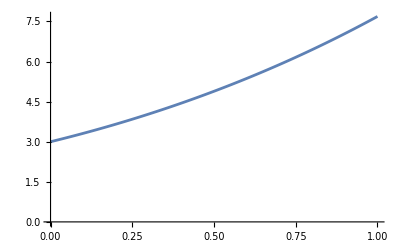

```mathematica
data2 = {{0,3},{0.01,3.03},{0.02,3.0603},{0.03,3.0909},{0.04,3.1218},{0.05,3.153},{0.06,3.1845},{0.07,3.21631},{0.08,3.24843},{0.09,3.28085},{0.1,3.31358},{0.11,3.34661},{0.12,3.37996},{0.13,3.41361},{0.14,3.44758},{0.15,3.48186},{0.16,3.51645},{0.17,3.55136},{0.18,3.58659},{0.19,3.62213},{0.2,3.65799},{0.21,3.69417},{0.22,3.73067},{0.23,3.76749},{0.24,3.80464},{0.25,3.84211},{0.26,3.8799},{0.27,3.91803},{0.28,3.95648},{0.29,3.99526},{0.3,4.03437},{0.31,4.07381},{0.32,4.11359},{0.33,4.1537},{0.34,4.19415},{0.35,4.23494},{0.36,4.27606},{0.37,4.31753},{0.38,4.35933},{0.39,4.40148},{0.4,4.44398},{0.41,4.48681},{0.42,4.53},{0.43,4.57354},{0.44,4.61742},{0.45,4.66166},{0.46,4.70625},{0.47,4.7512},{0.48,4.7965},{0.49,4.84216},{0.5,4.88819},{0.51,4.93457},{0.52,4.98131},{0.53,5.02842},{0.54,5.0759},{0.55,5.12374},{0.56,5.17195},{0.57,5.22054},{0.58,5.26949},{0.59,5.31882},{0.6,5.36853},{0.61,5.41862},{0.62,5.46908},{0.63,5.51993},{0.64,5.57116},{0.65,5.62277},{0.66,5.67478},{0.67,5.72717},{0.68,5.77995},{0.69,5.83313},{0.7,5.8867},{0.71,5.94066},{0.72,5.99503},{0.73,6.04979},{0.74,6.10496},{0.75,6.16054},{0.76,6.21652},{0.77,6.27291},{0.78,6.32971},{0.79,6.38692},{0.8,6.44455},{0.81,6.50259},{0.82,6.56106},{0.83,6.61995},{0.84,6.67926},{0.85,6.73899},{0.86,6.79916},{0.87,6.85975},{0.88,6.92078},{0.89,6.98224},{0.9,7.04415},{0.91,7.10649},{0.92,7.16927},{0.93,7.2325},{0.94,7.29618},{0.95,7.3603},{0.96,7.42488},{0.97,7.48991},{0.98,7.5554},{0.99,7.62135},{1,7.68777}}
ListPlot[data2, Joined->True]
```

```mathematica
Grid[Table[{t,f[t]},table],Frame->All]
```

0. | {3.}
0.01 | {3.03015}
0.02 | {3.0606}
0.03 | {3.09135}
0.04 | {3.12241}
0.05 | {3.15377}
0.06 | {3.18544}
0.07 | {3.21741}
0.08 | {3.24969}
0.09 | {3.28227}
0.1 | {3.31517}
0.11 | {3.34838}
0.12 | {3.3819}
0.13 | {3.41573}
0.14 | {3.44987}
0.15 | {3.48433}
0.16 | {3.51911}
0.17 | {3.5542}
0.18 | {3.58962}
0.19 | {3.62535}
0.2 | {3.6614}
0.21 | {3.69778}
0.22 | {3.73448}
0.23 | {3.7715}
0.24 | {3.80885}
0.25 | {3.84653}
0.26 | {3.88453}
0.27 | {3.92286}
0.28 | {3.96153}
0.29 | {4.00053}
0.3 | {4.03986}
0.31 | {4.07953}
0.32 | {4.11953}
0.33 | {4.15987}
0.34 | {4.20055}
0.35 | {4.24157}
0.36 | {4.28293}
0.37 | {4.32463}
0.38 | {4.36668}
0.39 | {4.40908}
0.4 | {4.45182}
0.41 | {4.49492}
0.42 | {4.53836}
0.43 | {4.58216}
0.44 | {4.62631}
0.45 | {4.67081}
0.46 | {4.71567}
0.47 | {4.76089}
0.48 | {4.80647}
0.49 | {4.85242}
0.5 | {4.89872}
0.51 | {4.94539}
0.52 | {4.99243}
0.53 | {5.03983}
0.54 | {5.08761}
0.55 | {5.13575}
0.56 | {5.18427}
0.57 | {5.23317}
0.58 | {5.28244}
0.59 | {5.33209}
0.6 | {5.38212}
0.61 | {5.43253}
0.62 | {5.48333}
0.63 | {5.53451}
0.64 | {5.58608}
0.65 | {5.63804}
0.66 | {5.69039}
0.67 | {5.74314}
0.68 | {5.79628}
0.69 | {5.84982}
0.7 | {5.90375}
0.71 | {5.95809}
0.72 | {6.01283}
0.73 | {6.06798}
0.74 | {6.12354}
0.75 | {6.1795}
0.76 | {6.23588}
0.77 | {6.29267}
0.78 | {6.34987}
0.79 | {6.4075}
0.8 | {6.46554}
0.81 | {6.52401}
0.82 | {6.5829}
0.83 | {6.64222}
0.84 | {6.70197}
0.85 | {6.76215}
0.86 | {6.82276}
0.87 | {6.88381}
0.88 | {6.9453}
0.89 | {7.00723}
0.9 | {7.0696}
0.91 | {7.13242}
0.92 | {7.19569}
0.93 | {7.25941}
0.94 | {7.32358}
0.95 | {7.38821}
0.96 | {7.4533}
0.97 | {7.51884}
0.98 | {7.58486}
0.99 | {7.65133}
1. | {7.71828}

```mathematica
Column[table]
```

{0.,{3.}}
{0.01,{3.03015}}
{0.02,{3.0606}}
{0.03,{3.09135}}
{0.04,{3.12241}}
{0.05,{3.15377}}
{0.06,{3.18544}}
{0.07,{3.21741}}
{0.08,{3.24969}}
{0.09,{3.28227}}
{0.1,{3.31517}}
{0.11,{3.34838}}
{0.12,{3.3819}}
{0.13,{3.41573}}
{0.14,{3.44987}}
{0.15,{3.48433}}
{0.16,{3.51911}}
{0.17,{3.5542}}
{0.18,{3.58962}}
{0.19,{3.62535}}
{0.2,{3.6614}}
{0.21,{3.69778}}
{0.22,{3.73448}}
{0.23,{3.7715}}
{0.24,{3.80885}}
{0.25,{3.84653}}
{0.26,{3.88453}}
{0.27,{3.92286}}
{0.28,{3.96153}}
{0.29,{4.00053}}
{0.3,{4.03986}}
{0.31,{4.07953}}
{0.32,{4.11953}}
{0.33,{4.15987}}
{0.34,{4.20055}}
{0.35,{4.24157}}
{0.36,{4.28293}}
{0.37,{4.32463}}
{0.38,{4.36668}}
{0.39,{4.40908}}
{0.4,{4.45182}}
{0.41,{4.49492}}
{0.42,{4.53836}}
{0.43,{4.58216}}
{0.44,{4.62631}}
{0.45,{4.67081}}
{0.46,{4.71567}}
{0.47,{4.76089}}
{0.48,{4.80647}}
{0.49,{4.85242}}
{0.5,{4.89872}}
{0.51,{4.94539}}
{0.52,{4.99243}}
{0.53,{5.03983}}
{0.54,{5.08761}}
{0.55,{5.13575}}
{0.56,{5.18427}}
{0.57,{5.23317}}
{0.58,{5.28244}}
{0.59,{5.33209}}
{0.6,{5.38212}}
{0.61,{5.43253}}
{0.62,{5.48333}}
{0.63,{5.53451}}
{0.64,{5.58608}}
{0.65,{5.63804}}
{0.66,{5.69039}}
{0.67,{5.74314}}
{0.68,{5.79628}}
{0.69,{5.84982}}
{0.7,{5.90375}}
{0.71,{5.95809}}
{0.72,{6.01283}}
{0.73,{6.06798}}
{0.74,{6.12354}}
{0.75,{6.1795}}
{0.76,{6.23588}}
{0.77,{6.29267}}
{0.78,{6.34987}}
{0.79,{6.4075}}
{0.8,{6.46554}}
{0.81,{6.52401}}
{0.82,{6.5829}}
{0.83,{6.64222}}
{0.84,{6.70197}}
{0.85,{6.76215}}
{0.86,{6.82276}}
{0.87,{6.88381}}
{0.88,{6.9453}}
{0.89,{7.00723}}
{0.9,{7.0696}}
{0.91,{7.13242}}
{0.92,{7.19569}}
{0.93,{7.25941}}
{0.94,{7.32358}}
{0.95,{7.38821}}
{0.96,{7.4533}}
{0.97,{7.51884}}
{0.98,{7.58486}}
{0.99,{7.65133}}
{1.,{7.71828}}